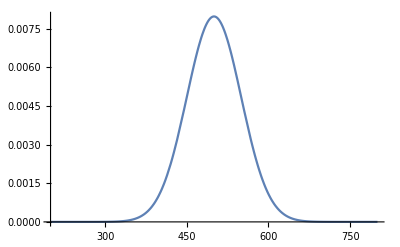

```mathematica
Plot[PDF[NormalDistribution[500,50]][x],{x,200,800}]
```

```mathematica
list = RandomVariate[NormalDistribution[500,50],10]
```

{600.773,485.765,469.713,472.4,530.091,505.302,546.341,542.283,446.111,453.973}

### 多臂老虎机

两个老虎机的正态分布：

```mathematica
laohuL = NormalDistribution[500,50]
laohuR = NormalDistribution[550,100]
```

ε - greedy

```mathematica
e=0.1;
currL=999;
currR=999;
count=;
```

```mathematica
randomL:=RandomVariate[laohuL]
randomR:=RandomVariate[laohuR]
```